```mathematica
Pdb Ids collected from different sources should be united for the following analysis
```

```mathematica
Path to project depends on machine
```

```mathematica
pathToProject="/media/my_extra_space/projects/1510GPCR/";
```

```mathematica
But other paths should not
```

```mathematica
pathToIdLists=pathToProject<>"inputs/idsLists/";
```

```mathematica
Import  ids from different format sources,unite them and name list variable 'givenIds'
```

```mathematica
fromPfam=Import[pathToIdLists<>"idsFromPFAM.csv","csv"];
fromRCSB=Import[pathToIdLists<>"idsFromRCSB.dat","table"];
fromRCSBgpcr=Import[pathToIdLists<>"idsFromRCSBgpcrReceptors.dat","table"];
fromOldPfam=Import[pathToIdLists<>"oldpfam.csv","csv"];
fromOldAll=Flatten@Import[pathToIdLists<>"oldAll.dat"];
givenIds=Union@(StringTake[#,4]&/@Drop[Union[Drop[fromPfamᵀ[[3]],1],Flatten@fromRCSB,Drop[fromOldPfam,1]ᵀ[[3]]],1]);
givenIds=Union[fromOldAll,givenIds];
givenIds=Union[ToUpperCase[#]&/@givenIds];
givenIds=ToUpperCase[#]&/@Union[givenIds,Union[StringTake[#,4]&/@Flatten@fromRCSBgpcr]];
```

```mathematica
Based on 'givenIds' list variable, create 'listOfPdbs' variable : id names, structures' short descriptions, exp. method and resolution
```

```mathematica
listOfPdbs={};
AppendTo[listOfPdbs,obj=Import["http://www.rcsb.org/pdb/rest/describePDB?structureId="<>#,"xml"];
{
#,
Cases[obj,XMLElement["PDB",{___,"title"->atrib_,___},___]:>atrib,∞],
Cases[obj,XMLElement["PDB",{___,"expMethod"->atrib_,___},___]:>atrib,∞],Cases[obj,XMLElement["PDB",{___,"resolution"->atrib_,___},___]:>atrib,∞]}
]&/@givenIds;
```

```mathematica
listOfPdbs=If[Length[Flatten@#]==4, Flatten@#,{}]&/@listOfPdbs;
listOfPdbs=Drop[Union[listOfPdbs],1];
```

```mathematica
Create 'thrown' list variable, fill it with the structures excluded from further analysis,and point the reasons for sieve (currently, method is the first sieving criteria)
```

```mathematica
thrown={};
listOfPdbs=If[#[[3]]≠"X-RAY DIFFRACTION",AppendTo[thrown,Flatten@{#[[1]],#[[2]],#[[3]], #[[4]]}];,#]&/@listOfPdbs;
listOfPdbs=Drop[Union@listOfPdbs,1];
```

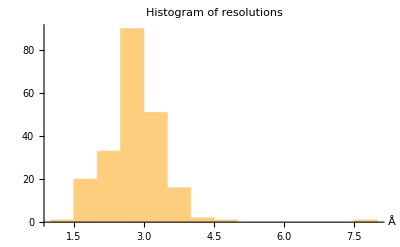

```mathematica
Histogram[ToExpression[#]&/@(listOfPdbsᵀ[[4]]), PlotRange->All, PlotLabel->Style["Histogram of resolutions",Black],AxesLabel->{"Å",None}]
```

```mathematica
Do[
If[ToExpression@(listOfPdbs[[n]][[4]])>4,Print[listOfPdbs[[n]]],];
,{n,1,Length@listOfPdbs}
];
```

{1YM7,G Protein-Coupled Receptor Kinase 2 (GRK2),X-RAY DIFFRACTION,4.50}

{2I36,Crystal structure of trigonal crystal form of ground-state rhodopsin,X-RAY DIFFRACTION,4.10}

{2I37,Crystal structure of a photoactivated rhodopsin,X-RAY DIFFRACTION,4.15}

{5DGY,Crystal structure of rhodopsin bound to visual arrestin,X-RAY DIFFRACTION,7.70}

```mathematica
pathToDump=pathToProject<>"dumps/";
Save[pathToDump<>"fromCollectingIdsForDeterminingChains.m",{pathToProject, listOfPdbs, thrown}];
```